```mathematica
(* Name *)
(* MATH2262 Analytic Geometry and Calculus II *)
(* Mathematica Project II *)

(* 1. Solve problems 65-67 on page 494 *)

(* Example *)
(* Find ∫1/(1+x^4)ⅆx *)
Integrate[1/(1+x^4),x] (* Press Shift + Enter *)
```

1/(4 √2)(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])

```mathematica
(* 2. Solve problems 81-86 on page 515 *)

(* Example *)
(* Explore ∫_1^∞ 1/x^p ⅆx *)
(* Evaluate the integral for various values of p*)
Table[{p,NIntegrate[1/x^p,{x,1,Infinity}]},{p,-2,2,0.1}]
```

{{-2.,2.13303041239557×10^83839},{-1.9,7.23149745687255×10^81044},{-1.8,2.45165540845636×10^78250},{-1.7,8.31171452062267×10^75455},{-1.6,2.81787554784575×10^72661},{-1.5,9.55329082023931×10^69866},{-1.4,3.23880043481127×10^67072},{-1.3,1.09803296622251×10^64278},{-1.2,3.72260168298007×10^61483},{-1.1,1.26205348256513×10^58689},{-1.,4.27867155412801×10^55894},{-0.9,1.45057483862689×10^53100},{-0.8,4.91780529506331×10^50305},{-0.7,1.66725688853268×10^47511},{-0.6,5.65241071078977×10^44716},{-0.5,1.91630618313424×10^41922},{-0.4,6.49674904279091×10^39127},{-0.3,2.20255763387306×10^36333},{-0.2,7.46721182954946×10^33538},{-0.1,2.53156837528713×10^30744},{0.,8.58263912306054×10^27949},{0.1,2.90972564812763×10^25155},{0.2,9.86468523955908×10^22360},{0.3,3.34437079791716×10^19566},{0.4,1.1338239145359×10^16772},{0.5,3.84394179620143×10^13977},{0.6,1.30319076380997×10^11183},{0.7,4.41813705028058×10^8388},{0.8,1.49785707027666×10^5594},{0.9,5.07810368365919×10^2799},{1.,191612.},{1.1,10.},{1.2,5.},{1.3,3.33333},{1.4,2.5},{1.5,2.},{1.6,1.66667},{1.7,1.42857},{1.8,1.25},{1.9,1.11111},{2.,1.}}

```mathematica
(* The integral converges when p>1 *)
```

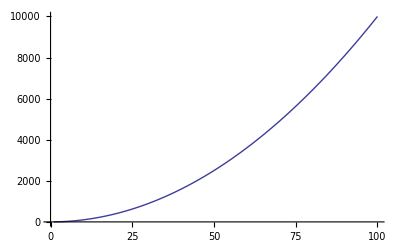
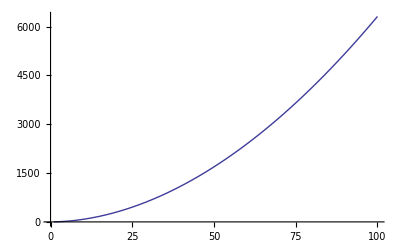
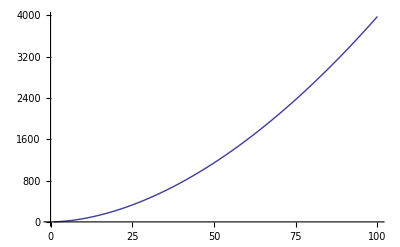
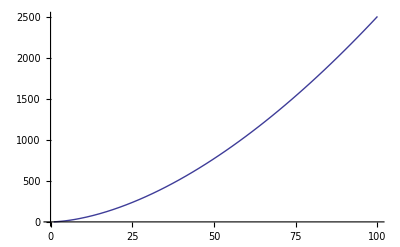
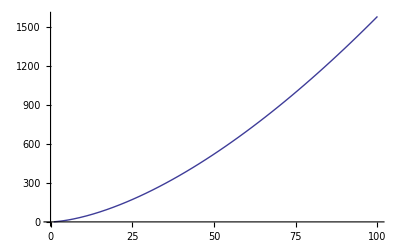
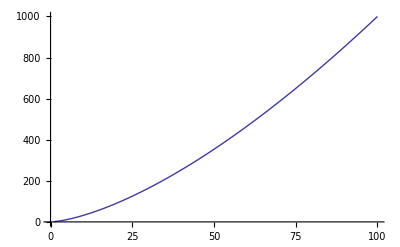
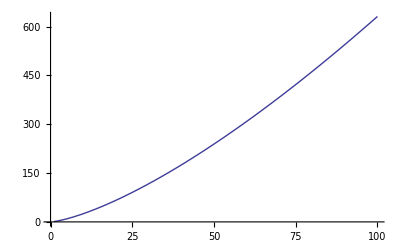
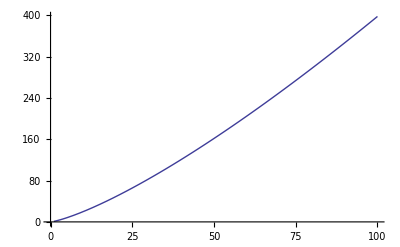
{{-2.,-Graphics-},{-1.9,-Graphics-},{-1.8,-Graphics-},{-1.7,-Graphics-},{-1.6,-Graphics-},{-1.5,-Graphics-},{-1.4,-Graphics-},{-1.3,-Graphics-},{-1.2,-Graphics-},{-1.1,-Graphics-},{-1.,-Graphics-},{-0.9,-Graphics-},{-0.8,-Graphics-},{-0.7,-Graphics-},{-0.6,-Graphics-},{-0.5,-Graphics-},{-0.4,-Graphics-},{-0.3,-Graphics-},{-0.2,-Graphics-},{-0.1,-Graphics-},{0.,-Graphics-},{0.1,-Graphics-},{0.2,-Graphics-},{0.3,-Graphics-},{0.4,-Graphics-},{0.5,-Graphics-},{0.6,-Graphics-},{0.7,-Graphics-},{0.8,-Graphics-},{0.9,-Graphics-},{1.,-Graphics-},{1.1,-Graphics-},{1.2,-Graphics-},{1.3,-Graphics-},{1.4,-Graphics-},{1.5,-Graphics-},{1.6,-Graphics-},{1.7,-Graphics-},{1.8,-Graphics-},{1.9,-Graphics-},{2.,-Graphics-}}

```mathematica
(* Graph the integrand for various values of p *)
Table[{p,Plot[1/x^p,{x,1,100},AxesOrigin->{0,0}]},{p,-2,2,0.1}]
```